```mathematica
data = Import["C:/Users/Brendan/Dropbox/Python projects/dissonance/Accordion_01_amplitudes_and_freqs.csv"];
amps = Import["C:/Users/Brendan/Dropbox/Python projects/dissonance/Accordion_01_amplitudes.csv"];
freqs = Import["C:/Users/Brendan/Dropbox/Python projects/dissonance/Accordion_01_freqs.csv"];
```

```mathematica
mypeaks = FindPeaks[data[[All,2]],.005,.1];
```

```mathematica
functions = List[];
```

```mathematica
Do[
AppendTo[functions, ContourPlot[x==Part[freqs,mypeaks[[i,1]]],{x,0,20000},{y,0,1.1}, ContourStyle->Red, BaseStyle->{Thickness[0.0000000001]}]],
{i,Length[mypeaks]}]
```

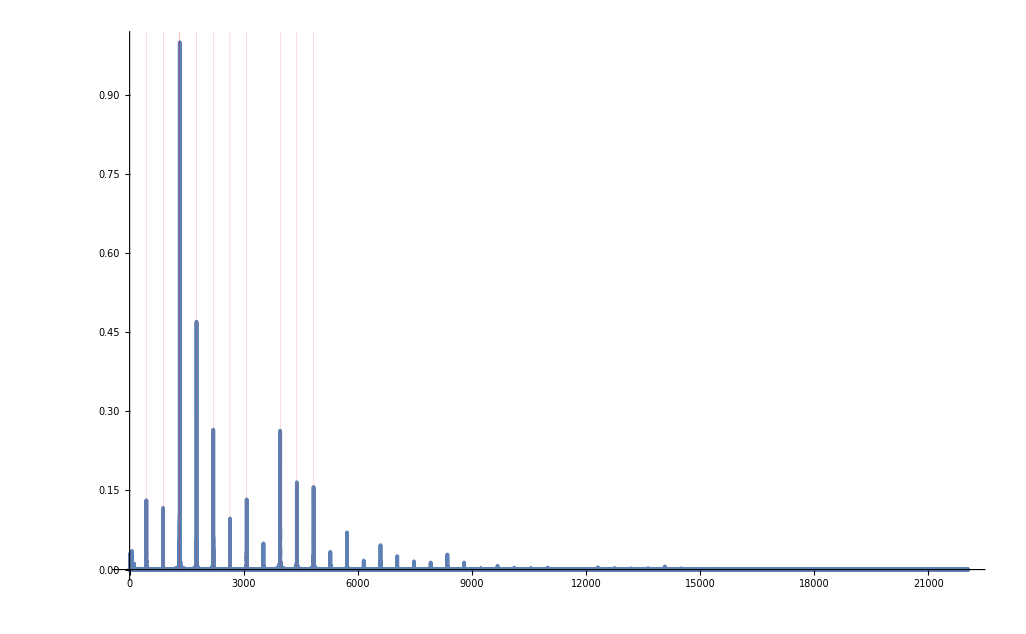

```mathematica
Show[ListLinePlot[data,PlotRange->All, PlotStyle->Thickness[.0027]],functions]
```